```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
yH=0;
results={};
f0vec=Table[10^eδ,{eδ,-10,-10}]//Reverse;
For[if0=1,if0≤Length[f0vec],if0+=1,
f0=f0vec[[if0]];
ϵ=10^-20;λ=Rationalize[638.5^2,0];δ=1/2;k=Rationalize[1.2383 √λ,0];q=k(1-δ);
U[G_]:=G^2/12;a=1/(√6);z[y_]:=(-1+ⅇ^(q ∫_0^y ⅇ^(a ϕ[yp])ⅆyp))/q;
icϕDs=Table[(D[ϕ[y],{y,n}]/.y->0)->(D[√(8/3)λ(z+1/k)^2,{z,n}]/.z->0),{n,0,2}];
icGDs=Table[(D[G[y],{y,n}]/.y->0)->(D[√(24λ)(z+1/k),{z,n}]/.z->0),{n,0,2}];
icDs=icϕDs~Join~icGDs~Join~{ϵ0->ϵ};
W=k (E^(a ϕ[y])(U[G[y]]+1-a ϕ[y])-1);
Vt=18(D[W,ϕ[y]]^2+D[W,G[y]]^2)-12 W^2-24k W//FullSimplify;
eqn1=3D[f[y](B[y]+q),y]-12f[y](B[y]+q)^2==Vt-12 k^2;
eqn2=B'[y]==1/6(ϕ'[y]^2+G'[y]^2);
eqn3=D[f[y]ϕ'[y],y]-4f[y](B[y]+q)ϕ'[y]==D[Vt,ϕ[y]];
eqn4=D[f[y]G'[y],y]-4f[y](B[y]+q)G'[y]==D[Vt,G[y]];
ic1=ϕ[ϵ]==(FullSimplify[Series[ϕ[z[ϵ0]],{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic2=ϕ'[ϵ]==(FullSimplify[Series[D[ϕ[z[y]],y]/.y->ϵ0,{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic3=G[ϵ]==(FullSimplify[Series[G[z[ϵ0]],{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic4=G'[ϵ]==(FullSimplify[Series[D[G[z[y]],y]/.y->ϵ0,{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic5=f[ϵ]==1;
ic6=B[ϵ]==((W/.y->0)+ϵ/6(ϕ'[0]^2+G'[0]^2))//.icDs;
(*ic1b=ϕ[ϵ]->(FullSimplify[Series[ϕ[z[ϵ0]],{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic2b=ϕ'[ϵ]->(FullSimplify[Series[D[ϕ[z[y]],y]/.y->ϵ0,{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic3b=G[ϵ]->(FullSimplify[Series[G[z[ϵ0]],{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic4b=G'[ϵ]->(FullSimplify[Series[D[G[z[y]],y]/.y->ϵ0,{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic5b=f[ϵ]->1;
ic6b=B[ϵ]->((W/.y->0)+ϵ/6(ϕ'[0]^2+G'[0]^2))//.icDs;*)
(*Reduce[{Vt==xVt,D[Vt,ϕ[y]]==dVtdϕ,D[Vt,G[y]]==dVtdG,ic1,ic2,ic3,ic4,ic5,ic6,y==ϵ}//.icDs/.{f[y]->1,f'[y]->0}]//N//FullSimplify
Solve[{eqn1,eqn2}//.(icDs~Join~{ic1b,ic2b,ic3b,ic4b,ic5b,ic6b}~Join~{f[0]->1,f'[0]->0,y->ϵ})]//FullSimplify//N
NSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6}//.{icDs~Join~{y->ϵ0}},Reals]*)
tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,B},{y,ϵ,5 10^-4},AccuracyGoal->∞,WorkingPrecision->50,Method->{"EventLocator","Event"->f[y]-f0,"EventAction":>Sow[y]}]];
 sol=First[{ϕ,G,f,B}/.First[tmp]];
{ymin,ymax}=First[sol[[1]]["Domain"]];
yH=tmp[[2,1,1]];
zH=(Exp[q NIntegrate[Exp[a sol[[1]][y]],{y,ymin,ymax}]]-1)/q;
TH=(-1/(4π)Exp[-a sol[[1]][y]]/(q zH+1)D[sol[[3]][y],y])/.y->yH;
Print[StringForm["f_0=``,T_H=``",f0,TH]];
AppendTo[results,{f0,TH}]]
```

NDSolve::ndsz: At y == 0.0001380579588690379932276742967692666481414964407636, step size is effectively zero; singularity or stiff system suspected.

f_0=1/10000000000,T_H=467.526

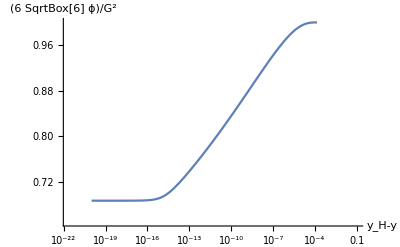

phi_By_G2.pdf

```mathematica
LogLinearPlot[(6 √6 sol[[1]][yH-y])/(sol[[2]][yH-y])^2,{y,ymin,yH},PlotRange->{{Automatic,10^-1},{0.65,Automatic}},AxesLabel->{Style["y_H-y",16],Style["(6 SqrtBox[6] ϕ)/G^2",16]}]
Export["phi_By_G2.pdf",%]
```

```mathematica
yH
```

0.0001380579588675712030463480064221749251602694022422

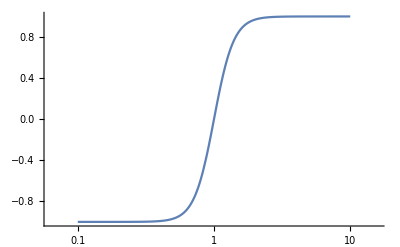

```mathematica
Plot[1-Exp[1/Log[1-x]],{x,0,1},PlotRange->All,AxesOrigin->{0,0},PlotPoints->200,AspectRatio->1];
LogLinearPlot[Tanh[3 Log[x^1]^1],{x,10^-1,10},PlotRange->All]
```

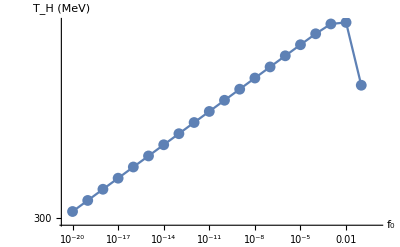

TH_vs_f0_comparison.pdf

```mathematica
Show[ListLogLogPlot[results],ListLogLogPlot[results,Joined->True],AxesLabel->{"f_0","T_H (MeV)"}]
Export["TH_vs_f0_comparison.pdf",%]
```

```mathematica
ϕdata=Table[{(Exp[k NIntegrate[Exp[a sol[[1]][y]],{y,ϵ,ypt}]]-1)/k,sol[[1]][ypt]},{ypt,ϵ,8 10^-5,5 10^-6}];
Gdata=Table[{(Exp[k NIntegrate[Exp[a sol[[1]][y]],{y,ϵ,ypt}]]-1)/k,sol[[2]][ypt]},{ypt,ϵ,8 10^-5,5 10^-6}];
```

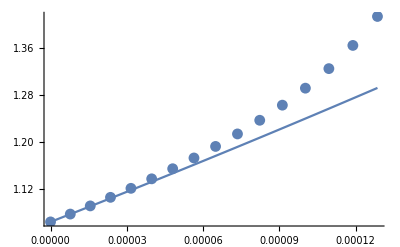

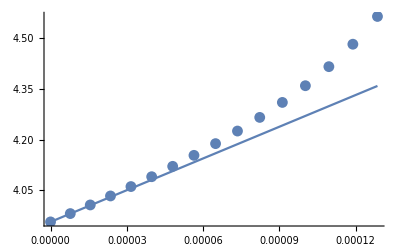

```mathematica
Show[ListPlot[ϕdata],Plot[√(8/3)λ(zpt+1/k)^2,{zpt,Min[ϕdata[[;;,1]]],Max[ϕdata[[;;,1]]]}]]
Show[ListPlot[Gdata],Plot[√(24λ)(zpt+1/k),{zpt,Min[Gdata[[;;,1]]],Max[Gdata[[;;,1]]]}]]
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
z[y_]:=(-1+ⅇ^(k ∫_0^y ⅇ^(a ϕ[yp])ⅆyp))/k;
ϵ=10^-15;λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];q=k;
U[G_]:=G^2/12;a=1/(√6);
icϕDs=Table[(D[ϕ[y],{y,n}]/.y->0)->(D[√(8/3)λ(z+1/k)^2,{z,n}]/.z->0),{n,0,2}];
icGDs=Table[(D[G[y],{y,n}]/.y->0)->(D[√(24λ)(z+1/k),{z,n}]/.z->0),{n,0,2}];
icDs=icϕDs~Join~icGDs~Join~{ϵ0->ϵ};
W=k (E^(a ϕ[y])(U[G[y]]+1-a ϕ[y])-1);
Vt=18(D[W,ϕ[y]]^2+D[W,G[y]]^2)-12 W^2-24k W//FullSimplify;
eqn1=3D[(B[y]+q),y]-12(B[y]+q)^2==Vt-12 k^2;
eqn2=B'[y]==1/6(ϕ'[y]^2+G'[y]^2);
eqn3=D[ϕ'[y],y]-4(B[y]+q)ϕ'[y]==D[Vt,ϕ[y]];
eqn4=D[G'[y],y]-4(B[y]+q)G'[y]==D[Vt,G[y]];
ic1=ϕ[ϵ]==(FullSimplify[Series[ϕ[z[ϵ0]],{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic2=ϕ'[ϵ]==(FullSimplify[Series[D[ϕ[z[y]],y]/.y->ϵ0,{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic3=G[ϵ]==(FullSimplify[Series[G[z[ϵ0]],{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
ic4=G'[ϵ]==(FullSimplify[Series[D[G[z[y]],y]/.y->ϵ0,{ϵ0,0,1}]//Normal,Assumptions->λ>0&&k>0]//.icDs);
(*ic6=B[ϵ]==((W/.y->0)+ϵ/6(ϕ'[ϵ]^2+G'[ϵ]^2))//.icDs;*)
ic6=B[ϵ]==(W/.y->ϵ)//.icDs;
```

```mathematica
sol=First[{ϕ,G,B}/.NDSolve[{eqn1,eqn3,eqn4,ic1,ic2,ic3,ic4,ic6},{ϕ,G,B},{y,ϵ,5 10^-4},AccuracyGoal->∞,WorkingPrecision->50,MaxSteps->∞]];
Plot[sol[[1]][y],{y,ϵ,4 10^-4}];
{ymin,ymax}=First[sol[[1]]["Domain"]];
```

NDSolve::ndsz: At y == 0.00040800085835635172467279988481723906410567344538243, step size is effectively zero; singularity or stiff system suspected.

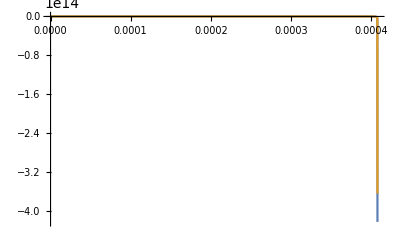

```mathematica
replacements={ϕ[y]->sol[[1]][y],G[y]->sol[[2]][y],B[y]->sol[[3]][y],ϕ'[y]->sol[[1]]'[y],G'[y]->sol[[2]]'[y],B'[y]->sol[[3]]'[y]};
Plot[{sol[[1]][y],sol[[2]][y]},{y,ymin,0.999*ymax},PlotRange->All];
Plot[W/(sol[[3]][y])/.replacements,{y,ymin,0.999*ymax},PlotRange->All];
Plot[{eqn1[[1]],eqn1[[2]]}/.replacements//Evaluate,{y,ymin,0.9999999ymax},PlotRange->All]
```

```mathematica
ϕdata=Table[{(Exp[k NIntegrate[Exp[a sol[[1]][y]],{y,ymin,ypt}]]-1)/k,sol[[1]][ypt]},{ypt,ymin,ymax,5 10^-6}];
Gdata=Table[{(Exp[k NIntegrate[Exp[a sol[[1]][y]],{y,ymin,ypt}]]-1)/k,sol[[2]][ypt]},{ypt,ymin,ymax,5 10^-6}];
```

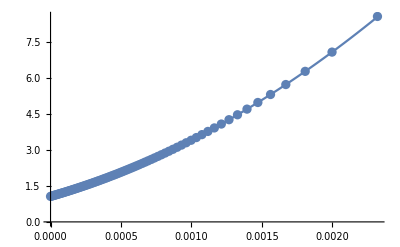

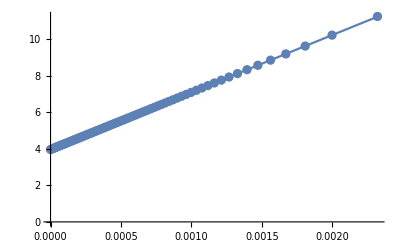

```mathematica
Show[ListPlot[ϕdata],Plot[√(8/3)λ(zpt+1/k)^2,{zpt,Min[ϕdata[[;;,1]]],Max[ϕdata[[;;,1]]]}]]
Show[ListPlot[Gdata],Plot[√(24λ)(zpt+1/k),{zpt,Min[Gdata[[;;,1]]],Max[Gdata[[;;,1]]]}]]
```

```mathematica
Integrate[Exp[-(2λ)/3(zp+1/k)^2]/(k zp+1),{zp,0,z},Assumptions->λ>0&&k>0&&z>0]
```

(-ExpIntegralEi[-(2 λ)/(3 k^2)]+ExpIntegralEi[-(2 (1+k z)^2 λ)/(3 k^2)])/(2 k)

```mathematica
FullSimplify[Out[1641]]//TraditionalForm
```

(-(2 (k z+1)^2 λ)/(3 k^2)--(2 λ)/(3 k^2))/(2 k)

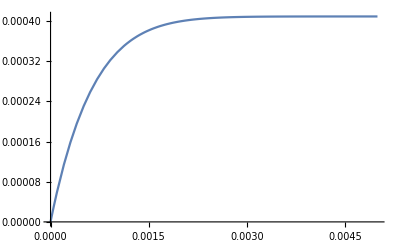

```mathematica
Plot[(-ExpIntegralEi[-(2 λ)/(3 k^2)]+ExpIntegralEi[-(2 (1+k z)^2 λ)/(3 k^2)])/(2 k)//.{λ->Rationalize[638.5^2,0],k->Rationalize[1.2383 √λ,0]},{z,0,200^-1},PlotRange->All]
```

```mathematica
Limit[(-ExpIntegralEi[-(2 λ)/(3 k^2)]+ExpIntegralEi[-(2 (1+k z)^2 λ)/(3 k^2)])/(2 k),z->∞,Assumptions->λ>0&&k>0&&z>0]
%//.{λ->Rationalize[638.5^2,0],k->Rationalize[1.2383 √λ,0]}//N
```

-ExpIntegralEi[-(2 λ)/(3 k^2)]/(2 k)

0.000409444

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
U[G_]:=G^2/12;a=1/(√6);
W[ϕ_,G_]:=k (E^(a ϕ)(U[G]+1-a ϕ)-1);
dWdϕ[ϕ_,G_]:=k (-a ⅇ^(a ϕ)+a ⅇ^(a ϕ) (1-a ϕ+U[G]));
dWdG[ϕ_,G_]:=ⅇ^(a ϕ) k U'[G];
Vt[ϕ_,G_]:=18(dWdϕ[ϕ,G]^2+dWdG[ϕ,G]^2)-12 W[ϕ,G]^2-24k W[ϕ,G]//FullSimplify;
eqn1=3D[f[y](B[y]+q),y]-12f[y](B[y]+q)^2==Vt[ϕ,G]-12 k^2;
eqn2=B'[y]==1/6(ϕ'[y]^2+G'[y]^2);
eqn3=D[f[y]ϕ'[y],y]-4f[y](B[y]+q)ϕ'[y]==D[Vt,ϕ[y]];
eqn4=D[f[y]G'[y],y]-4f[y](B[y]+q)G'[y]==D[Vt,G[y]];
Series[Vt[ϕ0+δϕ,G0+δG]-Vt[ϕ0,G0],{δϕ,0,1},{δG,0,1}]//Normal
```

-1/4 ⅇ^(√(2/3) ϕ0) G0 k^2 δG (12+G0^2-2 √6 ϕ0)+δϕ (-1/12 ⅇ^(√(2/3) ϕ0) G0 k^2 δG (6 √6+√6 G0^2-12 ϕ0)-1/48 ⅇ^(√(2/3) ϕ0) k^2 (12 √6 G0^2+√6 G0^4-240 ϕ0-24 G0^2 ϕ0+24 √6 ϕ0^2))

```mathematica
-1/4 ⅇ^(√(2/3) ϕ0) G0 k^2 δG (12+G0^2-2 √6 ϕ0)+δϕ (-1/12 ⅇ^(√(2/3) ϕ0) G0 k^2 δG (0)(6 √6+√6 G0^2-12 ϕ0)-1/48 ⅇ^(√(2/3) ϕ0) k^2 (12 √6 G0^2+√6 G0^4-240 ϕ0-24 G0^2 ϕ0+24 √6 ϕ0^2))//FullSimplify
```

-1/48 ⅇ^(√(2/3) ϕ0) k^2 (12 G0 δG (12+G0^2-2 √6 ϕ0)+δϕ (√6 G0^4+12 G0^2 (√6-2 ϕ0)+24 ϕ0 (-10+√6 ϕ0)))

```mathematica
(((3D[f[y]((B0[y]+δB[y])+k(1-δ)),y]-12f[y]((B0[y]+δB[y])+k(1-δ))^2)//FullSimplify)/.{f[y]->0,f'[y]->-s0}//Expand)==Vt[ϕ0+δϕ,G0+δG]-12 k^2
```

-3 k s0+3 k s0 δ-3 s0 B0[y]-3 s0 δB[y]==-12 k^2+Vt[δϕ+ϕ0,G0+δG]

```mathematica
(3D[f[y]((B0[y]+δB[y])+k(1-δ)),y]-12f[y]((B0[y]+δB[y])+k(1-δ))^2-(3D[(B0[y]+k),y]-12(B0[y]+k)^2)/.{f[y]->-s0 δy,f'[y]->-s0}//Expand)/.{δ^2->0,δ δB[y]->0,δ δy->0,δy δB[y]->0,δy δB[y]^2->0,δB[y]^2->0,δy δB'[y]->0(*,s0 δ->0,s0 δy->0,s0 δB[y]->0*)}
```

12 k^2-3 k s0+3 k s0 δ+12 k^2 s0 δy+24 k B0[y]-3 s0 B0[y]+24 k s0 δy B0[y]+12 B0[y]^2+12 s0 δy B0[y]^2-3 s0 δB[y]-3 B0'[y]-3 s0 δy B0'[y]

```mathematica
Out[4]/.{δ->0,δy->0,δB[y]->0,s0->0}
Out[4]-(Out[4]/.{δ->0,δy->0,δB[y]->0})
```

12 k^2+24 k B0[y]+12 B0[y]^2-3 B0'[y]

3 k s0 δ+12 k^2 s0 δy+24 k s0 δy B0[y]+12 s0 δy B0[y]^2-3 s0 δB[y]-3 s0 δy B0'[y]

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
a=1/(√6);U[G_]:=G^2/12;
W=k (E^(a ϕ[y])(U[G[y]]+1-a ϕ[y])-1);
Vt=18(D[W,ϕ[y]]^2+D[W,G[y]]^2)-12 W^2-24k W//FullSimplify;
W/.G[y]->0;
Vt/.G[y]->0;
D[Vt,G[y]]/.G[y]->0;
D[Vt,ϕ[y]]/.G[y]->0//FullSimplify;
eqn1=3D[f[y](B[y]+q),y]-12f[y](B[y]+q)^2==Vt-12 k^2;
eqn2=B'[y]==1/6(ϕ'[y]^2+G'[y]^2);
eqn3=D[f[y]ϕ'[y],y]-4f[y](B[y]+q)ϕ'[y]==D[Vt,ϕ[y]];
eqn4=D[f[y]G'[y],y]-4f[y](B[y]+q)G'[y]==D[Vt,G[y]];
eqn1yH=eqn1//.{y->yH,f[yH]->0}
eqn2yH=eqn2//.{y->yH,f[yH]->0}
eqn3yH=eqn3//.{y->yH,f[yH]->0}
eqn4yH=eqn4//.{y->yH,f[yH]->0}
Solve[{eqn1yH,eqn2yH,eqn3yH,eqn4yH},{f'[yH],B'[yH],ϕ'[yH],G'[yH]}]//FullSimplify
```

3 (q+B[yH]) f'[yH]==-12 k^2+1/16 k^2 (192+ⅇ^(√(2/3) ϕ[yH]) (-G[yH]^4+4 G[yH]^2 (-6+√6 ϕ[yH])+8 (-24+8 √6 ϕ[yH]-3 ϕ[yH]^2)))

B'[yH]==1/6 (G'[yH]^2+ϕ'[yH]^2)

f'[yH] ϕ'[yH]==1/16 k^2 (ⅇ^(√(2/3) ϕ[yH]) (4 √6 G[yH]^2+8 (8 √6-6 ϕ[yH]))+√(2/3) ⅇ^(√(2/3) ϕ[yH]) (-G[yH]^4+4 G[yH]^2 (-6+√6 ϕ[yH])+8 (-24+8 √6 ϕ[yH]-3 ϕ[yH]^2)))

f'[yH] G'[yH]==1/16 ⅇ^(√(2/3) ϕ[yH]) k^2 (-4 G[yH]^3+8 G[yH] (-6+√6 ϕ[yH]))

{{f'[yH]→(ⅇ^(√(2/3) ϕ[yH]) k^2 (-G[yH]^4+4 G[yH]^2 (-6+√6 ϕ[yH])+8 (-24+8 √6 ϕ[yH]-3 ϕ[yH]^2)))/(48 (q+B[yH])),B'[yH]→((q+B[yH])^2 (G[yH]^8-8 G[yH]^6 (-6+√6 ϕ[yH])+192 ϕ[yH]^2 (50-10 √6 ϕ[yH]+3 ϕ[yH]^2)+16 G[yH]^4 (45-17 √6 ϕ[yH]+9 ϕ[yH]^2)-192 G[yH]^2 (-18+ϕ[yH] (11 √6+ϕ[yH] (-16+√6 ϕ[yH])))))/(G[yH]^4-4 G[yH]^2 (-6+√6 ϕ[yH])+8 (24-8 √6 ϕ[yH]+3 ϕ[yH]^2))^2,ϕ'[yH]→((q+B[yH]) (√6 G[yH]^4+12 G[yH]^2 (√6-2 ϕ[yH])+24 ϕ[yH] (-10+√6 ϕ[yH])))/(G[yH]^4-4 G[yH]^2 (-6+√6 ϕ[yH])+8 (24-8 √6 ϕ[yH]+3 ϕ[yH]^2)),G'[yH]→(12 (q+B[yH]) G[yH] (12+G[yH]^2-2 √6 ϕ[yH]))/(G[yH]^4-4 G[yH]^2 (-6+√6 ϕ[yH])+8 (24-8 √6 ϕ[yH]+3 ϕ[yH]^2))}}

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
U[G_]:=G^2/12;a=1/(√6);

W=k (E^(a ϕ[y])(U[G[y]]+1-a ϕ[y])-1);
Vt=18(D[W,ϕ[y]]^2+D[W,G[y]]^2)-12 W^2-24k W//FullSimplify;
eqn1=3D[f[y](B[y]+q),y]-12f[y](B[y]+q)^2==Vt-12 k^2;
eqn2=B'[y]==1/6(ϕ'[y]^2+G'[y]^2);
eqn3=D[f[y]ϕ'[y],y]-4f[y](B[y]+q)ϕ'[y]==D[Vt,ϕ[y]];
eqn4=D[f[y]G'[y],y]-4f[y](B[y]+q)G'[y]==D[Vt,G[y]];
```

ⅇ^(√(2/3) ϕ[y]) k^2 (√6 G[y]^4+12 G[y]^2 (√6-2 ϕ[y])+24 ϕ[y] (-10+√6 ϕ[y]))+48 ((-4 (q+B[y]) f[y]+f'[y]) ϕ'[y]+f[y] ϕ''[y])==0

ⅇ^(√(2/3) ϕ[y]) k^2 G[y] (12+G[y]^2-2 √6 ϕ[y])+4 (-4 (q+B[y]) f[y]+f'[y]) G'[y]+4 f[y] G''[y]==0

```mathematica
DSolve[g'[x]/g[x]==-(T'[x]+q),g[x],x]//FullSimplify
```

{{g[x]→ⅇ^(-q x-T[x]) C[1]}}

```mathematica
U[G_]:=G^2/12;a=1/(√6); 
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1) E^(-a ϕ)); 
ς[ϕ_,G_]:=18 ((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24 k Ω[ϕ,G] (1) E^(-a ϕ); 
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1) 2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]); 
eqn1=3 (q z+1) (f'[z] β[z]+f[z] (a ϕ'[z] β[z]+β'[z]))-12 f[z] β[z]^2==ς[ϕ[z],G[z]]-(1) 12 E^(-2 a ϕ[z]) k^2; 
eqn2=6 (a ϕ'[z] β[z]+β'[z])==(q z+1) ((ϕ'[z])^2+(G'[z])^2); 
eqn3=f[z] (a (q z+1) (ϕ'[z])^2+(q-4 β[z]) ϕ'[z]+(q z+1) ϕ''[z])+(q z+1) f'[z] ϕ'[z]==1/(q z+1) (2 a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]); 
eqn4=f[z] (a (q z+1) ϕ'[z] G'[z]+(q-4 β[z]) G'[z]+(q z+1)G''[z])+(q z+1) f'[z] G'[z]==1/(q z+1) dςdG[ϕ[z],G[z]];
eqn1zH=eqn1//.{f[zH]->0,z->zH}//FullSimplify
eqn2zH=eqn2//.{f[zH]->0,z->zH}//FullSimplify
eqn3zH=eqn3//.{f[zH]->0,z->zH}//FullSimplify
eqn4zH=eqn4//.{f[zH]->0,z->zH}//FullSimplify
Print["z solution:"];
Solve[{eqn1zH,eqn2zH,eqn3zH,eqn4zH},{f'[zH],β'[zH],ϕ'[zH],G'[zH]}]//FullSimplify
rules1={G[z]->G[x],ϕ[z]->ϕ[x],β[z]->β[x],f[z]->f[x]};
rules2={ϕ'[z]->E^(-q x)ϕ'[x],G'[z]->E^(-q x)G'[x],β'[z]->E^(-q x)β'[x],f'[z]->E^(-q x)f'[x]};
rules3={f''[z]->ⅇ^(-2 q x) (2 q^2 f[x]-3 q f'[x]+f''[x]),G''[z]->ⅇ^(-2 q x) (2 q^2 G[x]-3 q G'[x]+G''[x]),ϕ''[z]->ⅇ^(-2 q x) (2 q^2 ϕ[x]-3 q ϕ'[x]+ϕ''[x]),β''[z]->ⅇ^(-2 q x) (2 q^2 β[x]-3 q β'[x]+β''[x])};
rules4={z->(-1+ⅇ^(q x))/q};
eqn1x=FullSimplify[((eqn1//FullSimplify)/.rules1/.rules2/.rules3/.rules4),Reals]
eqn2x=FullSimplify[((eqn2//FullSimplify)/.rules1/.rules2/.rules3/.rules4),Reals]
eqn3x=FullSimplify[((eqn3//FullSimplify)/.rules1/.rules2/.rules3/.rules4),Reals]
eqn4x=FullSimplify[((eqn4//FullSimplify)/.rules1/.rules2/.rules3/.rules4),Reals]
eqn1xH=eqn1x//.{f[xH]->0,x->xH}//FullSimplify
eqn2xH=eqn2x//.{f[xH]->0,x->xH}//FullSimplify
eqn3xH=eqn3x//.{f[xH]->0,x->xH}//FullSimplify
eqn4xH=eqn4x//.{f[xH]->0,x->xH}//FullSimplify
Print["x solution:"];
Solve[{eqn1xH,eqn2xH,eqn3xH,eqn4xH},{f'[xH],β'[xH],ϕ'[xH],G'[xH]}]//FullSimplify
```

k^2 (G[zH]^2 (24+G[zH]^2)-4 √6 (16+G[zH]^2) ϕ[zH]+24 ϕ[zH]^2)+48 (4 k^2+(1+q zH) β[zH] f'[zH])==0

6 β'[zH]+√6 β[zH] ϕ'[zH]==(1+q zH) (G'[zH]^2+ϕ'[zH]^2)

(1+q zH) f'[zH] ϕ'[zH]==-(k^2 (G[zH]^2 (12+G[zH]^2)-4 √6 (10+G[zH]^2) ϕ[zH]+24 ϕ[zH]^2))/(8 √6 (1+q zH))

(1+q zH) f'[zH] G'[zH]==-(k^2 G[zH] (12+G[zH]^2-2 √6 ϕ[zH]))/(4+4 q zH)

z solution:

{{f'[zH]→-(k^2 (G[zH]^4-4 G[zH]^2 (-6+√6 ϕ[zH])+8 (24-8 √6 ϕ[zH]+3 ϕ[zH]^2)))/(48 (1+q zH) β[zH]),β'[zH]→(12 β[zH]^2 (G[zH]^10+G[zH]^8 (44-6 √6 ϕ[zH])+16 G[zH]^6 (48-10 √6 ϕ[zH]+3 ϕ[zH]^2)+32 G[zH]^4 (192+ϕ[zH] (-20 √6+3 ϕ[zH] (-10+√6 ϕ[zH])))+192 G[zH]^2 (96+ϕ[zH] (80 √6-3 ϕ[zH] (88+3 ϕ[zH] (-4 √6+ϕ[zH]))))+384 ϕ[zH] (320 √6+ϕ[zH] (-1072+ϕ[zH] (208 √6+3 ϕ[zH] (-34+√6 ϕ[zH]))))))/((1+q zH) (G[zH]^12-12 G[zH]^10 (-6+√6 ϕ[zH])-7077888 (-1+√6 ϕ[zH])+24 G[zH]^8 (96-32 √6 ϕ[zH]+15 ϕ[zH]^2)-192 G[zH]^6 (-216+ϕ[zH] (108 √6+ϕ[zH] (-102+5 √6 ϕ[zH])))+1536 ϕ[zH]^2 (10944+ϕ[zH] (-2176 √6+9 ϕ[zH] (152-8 √6 ϕ[zH]+ϕ[zH]^2)))+576 G[zH]^4 (768+ϕ[zH] (-512 √6+ϕ[zH] (728-72 √6 ϕ[zH]+15 ϕ[zH]^2)))-2304 G[zH]^2 (-1152+ϕ[zH] (960 √6+ϕ[zH] (-1824+ϕ[zH] (272 √6+3 ϕ[zH] (-38+√6 ϕ[zH]))))))),ϕ'[zH]→(β[zH] (√6 G[zH]^4+12 G[zH]^2 (√6-2 ϕ[zH])+24 ϕ[zH] (-10+√6 ϕ[zH])))/((1+q zH) (G[zH]^4-4 G[zH]^2 (-6+√6 ϕ[zH])+8 (24-8 √6 ϕ[zH]+3 ϕ[zH]^2))),G'[zH]→(12 G[zH] β[zH] (12+G[zH]^2-2 √6 ϕ[zH]))/((1+q zH) (G[zH]^4-4 G[zH]^2 (-6+√6 ϕ[zH])+8 (24-8 √6 ϕ[zH]+3 ϕ[zH]^2)))}}

k^2 (G[x]^2 (24+G[x]^2)-4 √6 (16+G[x]^2) ϕ[x]+24 ϕ[x]^2)+8 (24 k^2+6 β[x] f'[x]+f[x] (-24 β[x]^2+6 β'[x]+√6 β[x] ϕ'[x]))==0

G'[x]^2+ϕ'[x]^2==6 β'[x]+√6 β[x] ϕ'[x]

k^2 (√6 G[x]^4+12 G[x]^2 (√6-2 ϕ[x])+24 ϕ[x] (-10+√6 ϕ[x]))+8 (6 (-2 f[x] (q+2 β[x])+f'[x]) ϕ'[x]+√6 f[x] ϕ'[x]^2+6 f[x] (2 q^2 ϕ[x]+ϕ''[x]))==0

3 k^2 G[x]^3+2 G'[x] (6 f'[x]+f[x] (-12 q-24 β[x]+√6 ϕ'[x]))+12 f[x] G''[x]==6 G[x] (-4 q^2 f[x]+k^2 (-6+√6 ϕ[x]))

k^2 (G[xH]^2 (24+G[xH]^2)-4 √6 (16+G[xH]^2) ϕ[xH]+24 ϕ[xH]^2)+48 (4 k^2+β[xH] f'[xH])==0

G'[xH]^2+ϕ'[xH]^2==6 β'[xH]+√6 β[xH] ϕ'[xH]

k^2 (√6 G[xH]^4+12 G[xH]^2 (√6-2 ϕ[xH])+24 ϕ[xH] (-10+√6 ϕ[xH]))+48 f'[xH] ϕ'[xH]==0

k^2 G[xH] (12+G[xH]^2-2 √6 ϕ[xH])+4 f'[xH] G'[xH]==0

x solution:

{{f'[xH]→-(k^2 (G[xH]^4-4 G[xH]^2 (-6+√6 ϕ[xH])+8 (24-8 √6 ϕ[xH]+3 ϕ[xH]^2)))/(48 β[xH]),β'[xH]→(12 β[xH]^2 (G[xH]^10+G[xH]^8 (44-6 √6 ϕ[xH])+16 G[xH]^6 (48-10 √6 ϕ[xH]+3 ϕ[xH]^2)+32 G[xH]^4 (192+ϕ[xH] (-20 √6+3 ϕ[xH] (-10+√6 ϕ[xH])))+192 G[xH]^2 (96+ϕ[xH] (80 √6-3 ϕ[xH] (88+3 ϕ[xH] (-4 √6+ϕ[xH]))))+384 ϕ[xH] (320 √6+ϕ[xH] (-1072+ϕ[xH] (208 √6+3 ϕ[xH] (-34+√6 ϕ[xH]))))))/(G[xH]^12-12 G[xH]^10 (-6+√6 ϕ[xH])-7077888 (-1+√6 ϕ[xH])+24 G[xH]^8 (96-32 √6 ϕ[xH]+15 ϕ[xH]^2)-192 G[xH]^6 (-216+ϕ[xH] (108 √6+ϕ[xH] (-102+5 √6 ϕ[xH])))+1536 ϕ[xH]^2 (10944+ϕ[xH] (-2176 √6+9 ϕ[xH] (152-8 √6 ϕ[xH]+ϕ[xH]^2)))+576 G[xH]^4 (768+ϕ[xH] (-512 √6+ϕ[xH] (728-72 √6 ϕ[xH]+15 ϕ[xH]^2)))-2304 G[xH]^2 (-1152+ϕ[xH] (960 √6+ϕ[xH] (-1824+ϕ[xH] (272 √6+3 ϕ[xH] (-38+√6 ϕ[xH])))))),ϕ'[xH]→(β[xH] (√6 G[xH]^4+12 G[xH]^2 (√6-2 ϕ[xH])+24 ϕ[xH] (-10+√6 ϕ[xH])))/(G[xH]^4-4 G[xH]^2 (-6+√6 ϕ[xH])+8 (24-8 √6 ϕ[xH]+3 ϕ[xH]^2)),G'[xH]→(12 G[xH] β[xH] (12+G[xH]^2-2 √6 ϕ[xH]))/(G[xH]^4-4 G[xH]^2 (-6+√6 ϕ[xH])+8 (24-8 √6 ϕ[xH]+3 ϕ[xH]^2))}}